# Оконные функции своими руками

## Предисловие

В цифровой обработке сигналов оконные функции широко используются для ограничения сигнала во времени и их названия хорошо известны всем, кто так или иначе сталкивался с дискретным преобразованием Фурье: Ханна, Хэмминга, Блекмана, Харриса и прочие. Но являются ли они достаточными, можно ли  придумать что-то новое и есть ли в этом смысл?

В этой статье мы рассмотрим вывод новой оконной функции со свойствами, выводящими их на качественно новый уровень. Предполагается также, что читатель имеет общие представления о цифровой обработке сигналов и контексте обсуждаемого вопроса.

## Введение

Исторически первые оконные функции появлялись в процессе попыток улучшить их спектральные свойства снижением амплитуды боковых лепестков - поскольку при умножении сигнала на оконную функции происходит свёртка их спектров, что вносит некоторые ограничения для анализа. В то время, 50-ые года 20 века, вычислительные мощности не позволяли легко и непринужденно манипулировать символьными вычислениями, и подбор оптимальных параметров представлял достаточную сложность. Это одна из причин, по которой функции названы разными именами - они, а точнее, их спектральные свойства, изучались разными исследователями в течении достаточно длительного времени. Побочным эффектом от этого стало то, что сложившийся набор именованных оконных функций воспринимается как некоторый «стандартный набор», за пределами которого ничего найти уже не возможно; при названия их не несут никакой информации о её свойствах и предполагают их отдельное изучение и зазубривание.

## Классификация

Все оконные функции получаются произведением некоторой функции на прямоугольную, что гарантированно обеспечивает её ограничение во времени. Поэтому в первую очередь их можно классифицировать по функциям, которые в них используются:

1) сумма косинусов. Наиболее обширный класс по причине того, что их спектр легко вычислим и представляет из себя сумму взвешенных sinc-функций. Сюда входят Hann, Hamming, Blackman, Harris ...
2) кусочно-непрерывные полиномиальные. Получаются в результате свёртки простых функций - например, прямоугольной и треугольной. Их спектры при этом перемножаются и их нахождение так же не представляет особых сложностей. Сюда входят Dirichlet, Triangular, Parzen, Welch...
3) все прочие - с использованием экспонент, гауссиан, sinc и других, выбор конкретных функций в которых носит скорее идейный характер, нежели конкретно спектральные свойства.

Также их можно поделить по свойствам на краях:
1) отсутствие разрывов на краях - равенство нулю значений. Разрывы имеют Dirichlet, Hamming, Blackman-Harris. Не имеют - Triangular, Hann, Nuttal.
2) отсутствие разрывов 1-ой и прочих производных. 

Отдельного упоминания стоят ещё две оконные функции:
1) Кайзера, позволящей задавать ширину главного лепестка;
2) Дольфа-Чебышева, все боковые лепестки которой равны заданной амплитуде.
Обе они имеют разрывы на краях как значений, так и производных, а вычисления их сопряжены с некоторыми сложностями - функция Кайзера считается через специальную функцию (Бесселя), а Дольфа-Чебышева определяется в частотной области и считается через обратное дискретное преобразование Фурье. Особую сложность также представляет нахождение их аналитических первообразных.

Исследовать оконные функции на разрывы можно следующим простым кодом:

```mathematica
wins={DirichletWindow,HammingWindow,BlackmanWindow,BartlettHannWindow,BartlettWindow,BlackmanHarrisWindow,BlackmanNuttallWindow,BohmanWindow,ExactBlackmanWindow,FlatTopWindow,KaiserBesselWindow,LanczosWindow,NuttallWindow};
Table[{f,Table[Limit[D[f[x],{x,k}],x->1/2,Direction->"FromBelow"],{k,0,4}]},{f,wins}]
```

{{DirichletWindow,{1,0,0,0,0}},{HammingWindow,{2/23,0,(42 π^2)/23,0,-(168 π^4)/23}},{BlackmanWindow,{0,0,(18 π^2)/25,0,(312 π^4)/25}},{BartlettHannWindow,{0,-12/25,(38 π^2)/25,0,-(152 π^4)/25}},{BartlettWindow,{0,-2,0,0,0}},{BlackmanHarrisWindow,{3/50000,0,(2829 π^2)/25000,0,(82611 π^4)/6250}},{BlackmanNuttallWindow,{907/2500000,0,(192747 π^2)/1250000,0,(4172427 π^4)/312500}},{BohmanWindow,{0,0,0,-16 π^2,0}},{ExactBlackmanWindow,{8/1163,0,(880 π^2)/1163,0,(13640 π^4)/1163}},{FlatTopWindow,{-210527/500000000,0,-(51368417 π^2)/250000000,0,-(971789551 π^4)/62500000}},{KaiserBesselWindow,{1/500,0,(111 π^2)/250,0,(402 π^4)/25}},{LanczosWindow,{0,-2,8,8 (-6+π^2),-64 (-6+π^2)}},{NuttallWindow,{0,0,(1494 π^2)/15625,0,(199848 π^4)/15625}}}

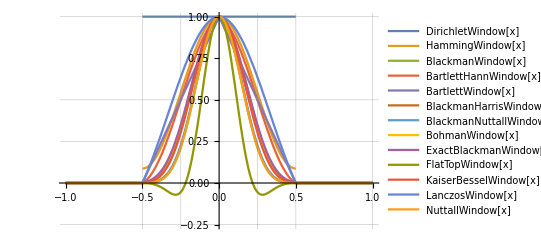

```mathematica
Plot[Evaluate[Through[wins[x]]],{x,-1,1},PlotRange->{-0.25,1},GridLines->{{-0.5,-0.25,0.25,0.5,1}},AspectRatio->5/8,PlotLegends->"Expressions"]
```

## Реверс инжиниринг

Посмотрим на определения функций Блэкмана и Наттела:

```mathematica
BlackmanWindow[x]//FunctionExpand
```

Piecewise[{{1/50 (21+25 Cos[2 π x]+4 Cos[4 π x]), -1/2≤x≤1/2}, {0, True}}]

```mathematica
NuttallWindow[x]//FunctionExpand
```

Piecewise[{{(88942+121849 Cos[2 π x]+36058 Cos[4 π x]+3151 Cos[6 π x])/250000, -1/2≤x≤1/2}, {0, True}}]

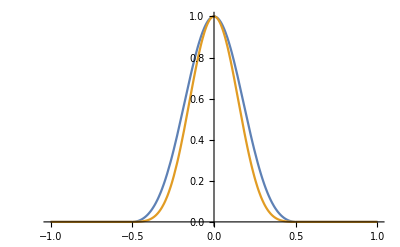

```mathematica
Plot[{BlackmanWindow[x],NuttallWindow[x]},{x,-1,1}]
```

Они представляют из себя суммы из 3-х и 4-х косинусоид с чётными частотами (начиная с нуля) и некоторыми коэффициентами. Откуда взялись эти коэффициенты? Вряд ли они были подобраны вручную, по крайней мере, каждый по отдельности - ведь существуют граничные условия, которым окна должны соответствовать вне зависимости от их спектральных свойств - как минимум, равенство единице в центре.

Попробуем «изобрести» функцию Блэкмана самостоятельно. Для этого определим функцию с пока ещё неизвестными коэффициентами

```mathematica
f=Function[x,a+ b Cos[2 Pi x]+ c Cos[4 Pi x]];
```

и составим систему уравнений, определяющих граничные условия - равенства единице в центре, нулю на краях, и равенства нулю производных на краях:

```mathematica
ss=Solve[{
f[0]==1,
f[1/2]==0,
f'[1/2]==0
},{a,b,c}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{b→1/2,c→1/2-a}}

Решение нашлось, но не одно, а множество - в зависимости от коэффициента a, о чём Wolfram нас учтиво предупредил. Теперь из найденного решения зададим новую функцию, зависящую от неизвестного коэффициента:

```mathematica
hx=Function[{x,a},Piecewise[{{f[x]/.ss[[1]],-1/2<x<1/2}},0]//Evaluate]
```

Function[{x,a},Piecewise[{{a+1/2 Cos[2 π x]+(1/2-a) Cos[4 π x], -1/2<x<1/2}, {0, True}}]]

[примечание]Ключевое слово Piecewise здесь определяет кусочно-непрерывную функцию, а постфиксный вызов Evaluate указывает, что необходимо сделать все возможные подстановки и вычисления, прежде чем определять тело функции.

Легко видеть, что при a=0.42 получим функцию Блэкмана. Но почему именно 0.42?

Для ответа на этот вопрос нам нужно построить её спектр. Аналитическое преобразование Фурье - не самая простая задача, но Wolfram справляется и с ней, избавляя нас от рутинной работы.

```mathematica
hw=Function[{w,a},FourierTransform[hx[x,a],x,w]//#/Limit[#,w->0]&//Simplify//Evaluate]
```

Function[{w,a},(4 π^2 (32 a π^2+3 w^2-8 a w^2) Sin[w/2])/(a (64 π^4 w-20 π^2 w^3+w^5))]

[примечание]В отличие от многих других операций, в команде FourierTransform нужно указывать не одну переменную, а две - в том числе и для того, чтобы не путаться, в какой области находится определение функции - временном или частотном. Традиционно для частотной области используется переменная w. Здесь мы заодно нормировали функцию к единице в центре координат - но не прямой подстановкой нуля в w, поскольку это вызывает деление на ноль, а через нахождение предела.

```mathematica
Manipulate[
Plot[
hw[w,a]
,{w,-111,111},PlotRange->All,GridLines->Automatic]
,{{a,0.45},0.4,0.5}]
```

В таком виде график функции пока ещё мало информативен, поскольку  спектр удобнее анализировать в логарифмическом масштабе. Добавив соответствующее преобразование в децибелы 20Log[10,|x|], получим тот самый привычный график спектра оконных функций:

```mathematica
Manipulate[
Plot[{
hw[w,a],
hw[w,0.42]
}//Abs//20Log[10,#]&//Evaluate
,{w,-111,111},PlotRange->{-120,0},GridLines->Automatic,PlotStyle->{Default,Thin},PlotPoints->50]
,{{a,0.409},0.3,0.5}]
```

В зависимости от параметра a меняется уровень боковых лепестков, и при a=0.42 он боле-менее минимальный и равномерный. При а=0.409 мы можем получить результат чуточку лучше, если под «лучше» понимать минимально возможный уровень боковых лепестков.

[примечание]Здесь можно вспомнить, что во времена становления теории ЦОС никаких Вольфрамов с интерактивными графиками не было и все эти вычисления и поиск оптимальных параметров производился вручную, ручкой на бумаге.

## Развитие

Очевидно подобная микрооптимизация вовсе не стоила затраченных усилий. Можно ли качественно улучшить свойства этого окна, не изменяя исходных данных?

Ранее мы рассматривали вывод оконных функций, суммирующихся в единицу, что позволяет восстанавливать исходный сигнал. Попробуем применить эту технику для нашего окна и посмотрим, как она отразится на спектре.

Определим вспомогательную функцию для построения перекрывающихся окон с учётом границ изменения аргумента в диапазоне от -1/2 до 1/2:

```mathematica
OverlapShape[f_,x_,a_,t_]:=(f[(1+2 t x)/(-2+2 t), a]-f[(-1+2 t x)/(-2+2 t),a])/2
```

Находим первообразную для нашего окна, смещаем её к центру координат и масштабируем к единице:

```mathematica
hsx=Function[{x,a},Integrate[hx[x,a],x]//#-(#/.x->0)&//#/(#/.x->1/2)&//Simplify//Evaluate]
```

Function[{x,a},Piecewise[{{-1, x≤-1/2}, {1, 2 x>1}, {(8 a π x+2 Sin[2 π x]+(1-2 a) Sin[4 π x])/(4 a π), True}}]]

```mathematica
Manipulate[
Plot[
hsx[x,a]
,{x,-1,1},PlotRange->All,GridLines->Automatic]
,{a,0.4,0.5}]
```

Как видим, Wolfram здесь тоже справился самостоятельно и нам не пришлось вручную задавать кусочно-непрерывное определение первообразной. Теперь вид нашего окна зависит не только от переменной <i>a</i>, но от степени перекрытия - и по мере его увеличения будет стремится к форме производной:

```mathematica
Manipulate[
Plot[
OverlapShape[hsx,x,a,t]
,{x,-1,1},PlotRange->All,GridLines->Automatic]
,{{a,0.404},0.4,0.5},{{t,4},3,11}]
```

И последний штрих - найти аналитическую функцию для спектра, чтобы определить оптимальное значение параметра a.

Здесь, если мы попробуем вычислить преобразование непосредственно, как в прошлый раз - то вгоним Wolfram в глубокую задумчивость. Есть несколько способов ускорить этот процесс:

- использовать дискретное преобразование вместо аналитического - наиболее простое. Но настоящий математик не будет применять численные методы там, где можно найти чисто аналитическое решение - и мы (пока) не будем; к тому же у него есть очевидные ограничения (по разрешению и ограничению спектра);

-  передавать в качестве параметра перекрытия конкретные значения и, глядя на результаты, попытаться увидеть закономерность и обобщить их. Вполне работающий вариант, но требующих дополнительных умственных и творческих усилий. Оставим его на крайний случай.

- производить вычисления непосредственно в частотном домене. Это возможно благодаря следующим свойствам преобразования Фурье:
1) оно линейно, т.е. сумма образов равно образу суммы;
2) интегрирование во временном домене равносильно делению на i w в частотном.
3) смещение во времени равносильно модуляцией комплексной синусоидой.
(подробнее в википедии [https://ru.wikipedia.org/wiki/%D0%9F%D1%80%D0%B5%D0%BE%D0%B1%D1%80%D0%B0%D0%B7%D0%BE%D0%B2%D0%B0%D0%BD%D0%B8%D0%B5_%D0%A4%D1%83%D1%80%D1%8C%D0%B5#%D0%A1%D0%B2%D0%BE%D0%B9%D1%81%D1%82%D0%B2%D0%B0])
или тут [http://ru.dsplib.org/content/fourier_transform_prop/fourier_transform_prop.html]

Таким образом, имея спектр hw произвольной оконной функции, мы можем получить из него спектр hwo суммирующейся в единицу функции с перекрытием t:

```mathematica
hwo=Function[{w,a,t},hw[w,a] Sin[w/(2-2 t)]/w//(#/.w->w (t-1)/t)&//#/Limit[#,w->0]&//FullSimplify//Evaluate]
```

Function[{w,a,t},(8 π^2 t^4 (32 a π^2 t^2-(-3+8 a) (-1+t)^2 w^2) Sin[w/(2 t)] Sin[((-1+t) w)/(2 t)])/(a (-1+t) w^2 (64 π^4 t^4-20 π^2 (-1+t)^2 t^2 w^2+(-1+t)^4 w^4))]

Теперь можно посмотреть, как меняется спектр в динамике:

```mathematica
Manipulate[
Plot[{
hwo[w,a,t]//Abs//20Log[10,#]&
},{w,-111,111},PlotRange->{-120,0},GridLines->Automatic,PlotPoints->100]
,{{a,0.404},0.3,0.5},{{t,4},2,6}]
```

Немного поигравшись с параметрами легко заметить, что «больше - не значит лучше», и оптимальная степень перекрытия для той функции находится в районе четырёх. Конкретно, для t=4 и a=0.404 мы получаем уровень боковых лепестков, не превышающий -80 дБ. Это очень даже неплохой результат - особенно учитывая, что функция приподнятого косинуса, традиционно используемая для суммируемых в единицу окон, даёт уровень лепестков примерно в -30 дБ. Ну а выписанная явном образом наша новая оконная функция будет выглядеть так:

```mathematica
OverlapShape[hsx,x,404/1000,4]//PiecewiseExpand//FullSimplify
```

Piecewise[{{(404 π (1-2 x)+375 Sin[1/3 (π-8 π x)]+36 Sin[1/3 (π+16 π x)])/(606 π), 1/4<x≤1/2}, {(404 (π+2 π x)+36 Sin[2/3 π (1+8 x)]+375 Sin[1/3 (π+8 π x)])/(606 π), -1/2<x≤-1/4}, {1/3+(√3 (125 Cos[(8 π x)/3]+12 Cos[(16 π x)/3]))/(202 π), -1/4<x≤1/4}, {0, True}}]

## Дальнейшее развитие

Что можно ещё сделать, чтобы ещё более снизить уровень боковых лепестков? Можно взять косинусы не с чётными, а с нечётными частотами (здесь для компактности решение системы уравнений внедрено непосредственно в определение функции):

```mathematica
hx1=Function[{x,a},
a Cos[1 Pi #]+ b Cos[3 Pi #]+ c Cos[5 Pi #]&//#[x]/.Solve[{
#[0]==1,
#[1/2]==0,
#'[1/2]==0,
#''[1/2]==0
},{a,b,c}][[1]]&//# UnitBox[x]&//Evaluate]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Function[{x,a},(a Cos[π x]+(5/8-a/2) Cos[3 π x]+(3/8-a/2) Cos[5 π x]) UnitBox[x]]

и с параметрами a=0.6628 и уровнем перекрытия 4.5 получить подавление в -90 дБ:

```mathematica
hwo1=Function[{w,a,t},FourierTransform[hx1[x,a],x,w] Sin[w/(2-2 t)]/w//(#/.w->w (t-1)/t)&//#/Limit[#,w->0]&//FullSimplify//Evaluate];
```

```mathematica
Manipulate[
Plot[{
hwo1[w,a+aa,t]//Abs//20Log[10,#]&
},{w,-100,100},PlotRange->{-150,0},GridLines->{Table[k,{k,-200,200,10}]},PlotPoints->100]
,{{a,0.6628},0,1},{{aa,0},-0.02,0.02},{{t,4.5},3,11}]
```

в явном виде

```mathematica
OverlapShape[Function[{x,a},Integrate[hx1[x,a],x]//#-(#/.x->0)&//#/(#/.x->1/2)&//Simplify//Evaluate],x,6628/10000,9/2]//PiecewiseExpand//FullSimplify
```

Piecewise[{{(21512+3670 Cos[1/14 (π+54 π x)]+327 Sin[1/7 π (2+45 x)]+24855 Sin[1/7 (π-9 π x)])/43024, 5/18<x≤1/2}, {(21512+24855 Sin[1/7 π (1+9 x)]+327 Sin[5/7 π (1+9 x)]+3670 Sin[3/7 (π+9 π x)])/43024, -1/2<x≤-5/18}, {(-3670 Sin[3/7 π (-1+9 x)]+24855 Sin[1/7 π (1+9 x)]+327 Sin[5/7 π (1+9 x)]+327 Sin[1/7 π (2+45 x)]+24855 Sin[1/7 (π-9 π x)]+3670 Sin[3/7 (π+9 π x)])/43024, -5/18<x≤5/18}, {0, True}}]

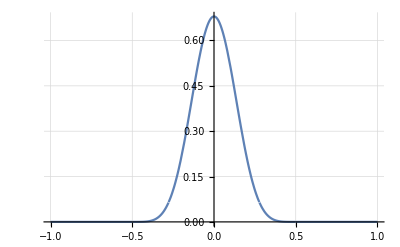

```mathematica
Plot[Piecewise[{{(21512+3670 Cos[1/14 (π+54 π x)]+327 Sin[1/7 π (2+45 x)]+24855 Sin[1/7 (π-9 π x)])/43024, 5/18<x≤1/2}, {(21512+24855 Sin[1/7 π (1+9 x)]+327 Sin[5/7 π (1+9 x)]+3670 Sin[3/7 (π+9 π x)])/43024, -1/2<x≤-5/18}, {1/43024(-3670 Sin[3/7 π (-1+9 x)]+24855 Sin[1/7 π (1+9 x)]+327 Sin[5/7 π (1+9 x)]+327 Sin[1/7 π (2+45 x)]+24855 Sin[1/7 (π-9 π x)]+3670 Sin[3/7 (π+9 π x)]), -5/18<x≤5/18}, {0, True}}],{x,-1,1},GridLines->Automatic]
```

Можно добавить ещё один косинус и увеличить количество нулевых производных:

```mathematica
hx2=Function[{x,a},
a Cos[1 Pi #] + b Cos[3 Pi #]+ c Cos[5 Pi #]+ d Cos[7 Pi #]&//#[x]/.Solve[{
#[0]==1,
#[1/2]==0,
#'[1/2]==0,
#''[1/2]==0,
#'''[1/2]==0,
#''''[1/2]==0
},{b,c,d}][[1]]&//# UnitBox[x]&//Evaluate]
```

Function[{x,a},(a Cos[π x]+1/80 (35-16 a) Cos[3 π x]+1/80 (35-48 a) Cos[5 π x]+1/40 (5-8 a) Cos[7 π x]) UnitBox[x]]

и с параметрами a=0.5862 и уровнем перекрытия 6.4 получить подавление в -110 дБ:

```mathematica
hwo2=Function[{w,a,t},FourierTransform[hx2[x,a],x,w] Sin[w/(2-2 t)]/w//(#/.w->w (t-1)/t)&//#/Limit[#,w->0]&//FullSimplify//Evaluate];
```

```mathematica
Manipulate[
Plot[{
hwo2[w,a+aa,t]//Abs//20Log[10,#]&
},{w,-100,100},PlotRange->{-150,0},GridLines->{Table[k,{k,-200,200,10}]},PlotPoints->100]
,{{a,0.5862},0,1},{{aa,0},-0.02,0.02},{{t,6.4},3,11}]
```

```mathematica
OverlapShape[Function[{x,a},Integrate[hx2[x,a],x]//#-(#/.x->0)&//#/(#/.x->1/2)&//Simplify//FullSimplify//Evaluate],x,5862/10000,64/10]//Simplify//PiecewiseExpand//Simplify
```

Piecewise[{{(2601344-560455 Cos[1/9 π (7-32 x)]-3077550 Sin[1/54 π (-5+64 x)]-90069 Sin[5/54 π (-5+64 x)]-5820 Sin[7/54 π (-5+64 x)])/5202688, 11/32<x≤1/2}, {(2601344+3077550 Sin[1/54 π (5+64 x)]+560455 Sin[1/18 π (5+64 x)]+90069 Sin[5/54 π (5+64 x)]+5820 Sin[7/54 π (5+64 x)])/5202688, -1/2<x≤-11/32}, {1/5202688(-560455 Cos[1/9 π (7-32 x)]-3077550 Sin[1/54 π (-5+64 x)]-90069 Sin[5/54 π (-5+64 x)]-5820 Sin[7/54 π (-5+64 x)]+3077550 Sin[1/54 π (5+64 x)]+560455 Sin[1/18 π (5+64 x)]+90069 Sin[5/54 π (5+64 x)]+5820 Sin[7/54 π (5+64 x)]), -11/32<x≤11/32}, {0, True}}]

```mathematica
OverlapShape[Function[{x,a},Integrate[hx2[x,a],x]//#-(#/.x->0)&//#/(#/.x->1/2)&//Simplify//FullSimplify//Evaluate],x,5862/10000,64/10]//Simplify
```

1/2 ((Piecewise[{{-1, x≤-1/2}, {1, 32 x>11}, {(3077550 Sin[1/54 π (5+64 x)]+560455 Sin[1/18 π (5+64 x)]+90069 Sin[5/54 π (5+64 x)]+5820 Sin[7/54 π (5+64 x)])/2601344, True}}])-(Piecewise[{{-1, x≤-11/32}, {1, 2 x>1}, {(560455 Cos[1/9 π (7-32 x)]+3077550 Sin[1/54 π (-5+64 x)]+90069 Sin[5/54 π (-5+64 x)]+5820 Sin[7/54 π (-5+64 x)])/2601344, True}}]))

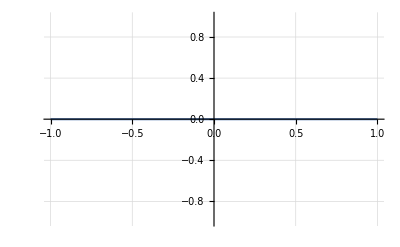

```mathematica
Plot[0,{x,-1,1},GridLines->Automatic]
```

Ещё более значительного снижения уровня боковых лепестков можно добиться, возведя Фурье-образ в квадрат и тем самым снизив уровень боковых лепестков сразу в 2 раза. Это позволяет избавится от увеличения количества параметров для их ручного подбора, но добавляет сложности в вычислении свёртки во временном домене. Ну и сама функция получается чуть более внушительной:

```mathematica
hx3=Function[{x,a},Convolve[hx1[x,a],hx1[x,a],x,y]/.y->2x//FullSimplify//Evaluate]
```

Function[{x,a},Piecewise[{{1/(7680 π)(3840 a^2 π (1+2 x) Cos[2 π x]+60 (5-4 a)^2 π (1+2 x) Cos[6 π x]+60 (3-4 a)^2 π (1+2 x) Cos[10 π x]+160 (15-32 a) a Sin[2 π x]+5 (-5+4 a) (-25+92 a) Sin[6 π x]-(-3+4 a) (-261+308 a) Sin[10 π x]), -1<2 x≤0}, {1/(7680 π)(3840 a^2 π (1-2 x) Cos[2 π x]-60 (5-4 a)^2 π (-1+2 x) Cos[6 π x]-60 (3-4 a)^2 π (-1+2 x) Cos[10 π x]+160 a (-15+32 a) Sin[2 π x]-5 (-5+4 a) (-25+92 a) Sin[6 π x]+(-3+4 a) (-261+308 a) Sin[10 π x]), 0<2 x<1}, {0, True}}]]

```mathematica
Manipulate[
Plot[
hx3[x,a]
,{x,-1,1},PlotRange->All,GridLines->Automatic]
,{a,0,2}]
```

```mathematica
hwo3=Function[{w,a,t},FourierTransform[hx3[x,a],x,w] Sin[w/(2-2 t)]/w//(#/.w->w (t-1)/t)&//#/Limit[#,w->0]&//FullSimplify//Evaluate];
```

$Aborted

```mathematica
Manipulate[
Plot[{
hwo3[w,a+aa,t]//Abs//20Log[10,#]&
},{w,-100,100},PlotRange->{-190,0},GridLines->{Table[k,{k,-200,200,10}]},PlotPoints->100]
,{{a,0.6718},0,1},{{aa,0},-0.02,0.02},{{t,10.23},3,11}]
```

Формулу в явном виде приводить не будем из-за её внушительного размера.

## Гипергеометрические оконные функции

Для обеспечения нужного количества нулей на границах нашей функции мы использовали поиск через решение системы уравнений с последующим интегрированием. Это не очень удобно - ведь нужно каждый раз менять количество уравнений. Может, есть более просто и красивое решение? Есть! И поможет нам в этом гипергеометрическая функция.

[вкратце о гипергеометрических функциях]
Из курса матанализа нам известно, что практически любую функцию можно разложить в степенной ряд. Гипергеометрические функции решают прямо противоположную задачу - определяют функцию через её степенной ряд, задавая конечный набор некоторых коэффициентов и правило вычисления произвольного члена ряда в зависимости от них. Это позволяет оперировать большим количеством функций без задания им явных имён - в том числе и уже известными.

Наше решение будет выглядеть следующим образом:

```mathematica
(2 z Gamma[(3+n)/2] Hypergeometric2F1[1/2,-n/2,3/2,z^2])/(√π Gamma[1+n/2])+a (  z+b z^3)(1-z^2)^(n/2)
```

где

```mathematica
z=Sin[(π x)/2]
```

Она состоит из суммы двух частей: первообразная от функции (1 - x^2)^(n/2), нормированной по амплитуде к точке (1,1) и функцией со свободными параметрами, помноженных на ту же (1 - x^2)^(n/2) для того, чтобы сохранить необходимое количество нулевых производных:

```mathematica
Manipulate[Plot[{(2 z Gamma[(3+n)/2] Hypergeometric2F1[1/2,-n/2,3/2,z^2])/(√π Gamma[1+n/2]),a (  z+b z^3)(1-z^2)^(n/2)},{z,-1.1,1.1},GridLines->Automatic],{{n,2},1,11,1},{{a,0.5},-1,1},{{b,0},-1,1}]
```

В зависимости от того, какую именно функцию мы выберем для корректировки формы, будут зависеть точность настройки и их влияние на распределение боковых лепестков - тут возможны варианты, требующие отдельных исследований. В данном случае функция a(z+b z^3) даёт вполне приемлемый вариант - и за счёт двух параметров позволяет делать более точную настройку.

В данном же случае формула интересна (и удобна) тем, что при чётных n упрощается до полинома, а при нечётных - до суммы полинома с арксинусом и квадратным корнем. Это делает итоговую формулу более компактной и более простой для вычислений.

Подбирать параметры здесь уже проще (и быстрее) через дискретное преобразование Фурье. Нам также потребуется дополнительное определение overlap-функции для работы с тремя параметрами:

```mathematica
OverlapShape[f_,x_,a_,b_,c_,t_]:=(f[-1+(2 t x)/(-1+t),a,b,c]-f[1+(2 t (-1+x))/(-1+t),a,b,c])/2
```

```mathematica
HypergeometricClip=Function[{x,n,a,b},Piecewise[{{-1,x≤-1},{1,x≥1}},(2 z Gamma[(3+n)/2] Hypergeometric2F1[1/2,-n/2,3/2,z^2])/(√π Gamma[1+n/2])+a(1-z^2)^(n/2) (  z+b z^3)/.z->Sin[x Pi/2]]//Simplify//Evaluate];
```

```mathematica
size=32;
pad=15;
Manipulate[
wfdata=Table[
OverlapShape[HypergeometricClip,x/size,n,a,b,t]
,{x,0,size+pad size,1}];

spectr=Fourier[wfdata]//Abs//20Log[10,#]&//#-#[[1]]&//#[[1;;(Length[#]+1)/2]]&;

ListLinePlot[{spectr},PlotRange->{-200,10},Filling->Bottom,GridLines->{Table[i,{i,0,1100,10}],Table[i,{i,-200,0,10}]},PlotStyle->{Hue[0.99, 0.6, 0.7],Hue[0.33, 0.6, 0.7],Hue[0.62, 0.6, 0.7]},ImageSize->Large]

,{{n,8},0,11,1},{{a,0.09},-0.3,0.3},{{b,-1},-2,2},{{t,8},2,11}]
```

В качестве примера, после подстановки параметров с картинки наша функция упростится до

```mathematica
(2 z Gamma[(3+n)/2] Hypergeometric2F1[1/2,-n/2,3/2,z^2])/(√π Gamma[1+n/2])+a(1-z^2)^(n/2) (  z+b z^3)/.{n->8,b->-1,a->9/100}//Simplify
```

(8163 z-11940 z^3+12330 z^5-7380 z^7+2315 z^9-288 z^11)/3200

## Инверсное окно Кайзера

Если задача суммирования окон в единицу не стоит, то наиболее оптимальным окном является окно Кайзера, позволяющее плавно регулировать ширину основного лепестка. Однако у него есть недостаток - поскольку оно выражается через функцию Бесселя

```mathematica
KaiserWindow[x,k]//FunctionExpand
```

Piecewise[{{BesselI[0,k √(1-2 x) √(1+2 x)]/BesselI[0,k], -1/2≤x≤1/2}, {0, True}}]

считать его за пределами математических пакетов несколько затруднительно. Можно, конечно, отдельно реализовать функцию Бесселя - а можно и поискать аппроксимацию через элементарные функции. И неожиданно оказалось, что используя для этого функцию спектра окна Кайзера (ограниченного во времени) можно получить результат даже чуточку лучше

```mathematica
InverseKaiserWindow=Function[{x,k},Piecewise[{{k Csch[k],Abs[x]==1/2}},Sinh[k √(1-4 x^2)]/(Sinh[k] √(1-4 x^2))]UnitBox[x]];
```

[примечание] В точках  ±.bd функция имеет особую точку, которая находится через предел.

Расплатой за такое хитрое решение оказалось невозможность выразить её спектр чисто аналитически - но это не так и важно, поскольку на практике мы в любом случае оперируем и анализируем данные в дискретном виде используя дискретное же преобразование Фурье. Ниже на графике можно сравнить их спектры, где красным - оригинальное окно Кайзера, зелёным - его аппроксимация:

```mathematica
size=32;
pad=15;
Manipulate[
wfdataK=Table[KaiserWindow[x/size-1/2,k]
,{x,0,size+pad size}];
wfdataIK=Table[InverseKaiserWindow[x/size-1/2,(k s)]
,{x,0,size+pad size}];
spectrK= Fourier[wfdataK]//Abs//20Log[10,#]&//#-#[[1]]&//#[[1;;(Length[#]+1)/2]]&;
spectrIK= Fourier[wfdataIK]//Abs//20Log[10,#]&//#-#[[1]]&//#[[1;;(Length[#]+1)/2]]&;

ListLinePlot[{spectrK,spectrIK},PlotRange->{-160,10},Filling->Bottom,GridLines->{Table[i,{i,0,1100,10}],Table[i,{i,-160,0,10}]},PlotStyle->{Hue[0.99, 0.6, 0.7],Hue[0.33, 0.6, 0.7],Hue[0.62, 0.6, 0.7]},ImageSize->Large]

,{{k,12},1,21},{{s,0.955},0.9,1.1}]
```

При том же уровне боковых лепестков ширина основного лепестка получается несколько уже. Для удобства пользования можно составить таблицу с ориентировочными значениями параметра для получения необходимого уровня подавления боковых лепестков:

```mathematica
{
{"-60 db","k=8.8"},
{"-90 db","k=11.36"},
{"-120 db","k=15.18"},
{"-150 db","k=18.88"}
}//Grid[#,Frame->All]&
```

-60 db | k=8.8
-90 db | k=11.36
-120 db | k=15.18
-150 db | k=18.88

Отдельной интересной задачей остаётся нахождение аппроксимации первообразной инверсного окна Кайзера. Пока что удалось только выразить его через степенной ряд, который довольно медленно сходится:

```mathematica
∑_(n=1)^∞ -(2^(1/2-n) k^(-1+n) x^(-1+2 n) ((-1)^n √-k BesselK[-1/2+n,-k]+√k BesselK[-1/2+n,k]))/((-1+2 n) √π Gamma[n]Sinh[k])
```

Возможно, специалисты в математике смогут подсказать более лучшее решение в комментариях.

## Заключение

Несмотря на то, что ЦОС является вполне себе сформировавшейся дисциплиной, в ней есть ещё куда развиваться и находить что-то новое - как минимум в существующей специальной и научной литературе вопросы построения суммирующихся в единицу оконных функций не рассматривается; а возможности современных систем компьютерной алгебры позволяют переосмыслить накопленные знания на качественно новом уровне.

Исходный документ со всеми вычислениями доступен [здесь].